# Determine the Mal-CoA Km for FabD Reaction

Import the FabD equations

```mathematica
ODEsRawFAS=Flatten[ToExpression[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/FAS","2020_fox_ODEs.csv"}]]]];
enzymeEqsFAS=Flatten[ToExpression[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/FAS","2020_fox_enzyme_totals.csv"}]]]];
kinParamsFAS=Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/FAS","2020_fox_kinetic_params.csv"}]];
kinParamsFAS=Symbol[StringReplace[ToString[#[[1]]],"_"->""]]->#[[2]]&/@kinParamsFAS;
enzymeConcsFAS=Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/FAS","FAS_enzyme_concentrations.csv"}]];
enzymeConcsFAS=Symbol[#[[1]]]->#[[2]]&/@enzymeConcsFAS;
ODEsFAS=ODEsRawFAS/.enzymeEqsFAS;

(* y4 => ACP, 
y8 => Mal-CoA,
y9 => CoA,
y10 => Mal-ACP,
y87 => ES1,
y88 => ES2,
y89 => ES3 *)

ODEsFabD=Join[{
y4'[t]==k23r y89[t]-k23f y88[t] y4[t],
y8'[t]==k21r y87[t]-k21f y8[t] (e2tot-y87[t]-y88[t]-y89[t]),
y9'[t]==k22f y87[t]-k22r y88[t] y9[t],
y10'[t]==k24f y89[t]-k24r y10[t] (e2tot-y87[t]-y88[t]-y89[t])
},ODEsFAS[[{87,88,89}]]]/.kinParamsFAS;
initsFabD={
y4[0]==y4zero,
y8[0]==y8zero,
y9[0]==0,
y10[0]==0,
y87[0]==0,
y88[0]==0,
y89[0]==0
};
eqs=Join[ODEsFabD,initsFabD]
```

{y4'[t]==-77.292 y4[t] y88[t]+3091.68 y89[t],y8'[t]==11397.9 y87[t]-189.965 y8[t] (e2tot-y87[t]-y88[t]-y89[t]),y9'[t]==60222.9 y87[t]-402.139 y88[t] y9[t],y10'[t]==-402.139 y10[t] (e2tot-y87[t]-y88[t]-y89[t])+1411.1 y89[t],y87'[t]==-71620.8 y87[t]+189.965 y8[t] (e2tot-y87[t]-y88[t]-y89[t])+402.139 y88[t] y9[t],y88'[t]==60222.9 y87[t]-77.292 y4[t] y88[t]+3091.68 y89[t]-402.139 y88[t] y9[t],y89'[t]==77.292 y4[t] y88[t]+402.139 y10[t] (e2tot-y87[t]-y88[t]-y89[t])-4502.78 y89[t],y4[0]==y4zero,y8[0]==y8zero,y9[0]==0,y10[0]==0,y87[0]==0,y88[0]==0,y89[0]==0}

Run titration experiments to determine the Km.

0.05

[S]: {0.931008}

[S]: {1.87467}

[S]: {4.75394}

[S]: {9.6369}

[S]: {19.5227}

[S]: {49.4105}

[S]: {99.36}

[S]: {199.331}

[S]: {499.313}

{{1,0.00328961},{2,0.00631407},{5,0.0140411},{10,0.0235508},{20,0.0351334},{50,0.048628},{100,0.0552097},{200,0.0590673},{500,0.061598}}

Calculated Km for Malonyl-CoA: 16.9601

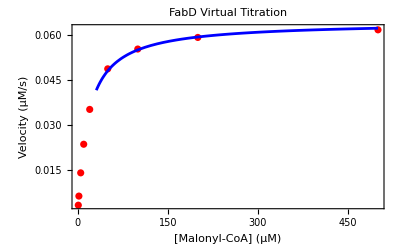

../results/virtual_titration_0_05.png

```mathematica
e2T=0.05
GetInitialVelocity[y8init_,e2T_]:=Module[{sol,tMax=0.1,y4tot=1000},
sol=NDSolve[eqs/.{y8zero->y8init,e2tot->e2T,y4zero->y4tot},{y8[t],y9[t],y10[t],y87[t],y88[t],y89[t]},{t,0,tMax}];
Print["[S]: ",y8[t]/.sol/.t->tMax/10];
y10[t]/.sol/.t->tMax/100]
testConcentrations={1,2,5,10,20,50,100,200,500};
data=Table[{c,GetInitialVelocity[c,e2T][[1]]},{c,testConcentrations}];
data
model=NonlinearModelFit[data,{(Vmax*S)/(Km+S),Km>0 && Vmax>0},{Vmax,Km},S];
Print["Calculated Km for Malonyl-CoA: ",Km/. model["BestFitParameters"]]
plot=Show[ListPlot[data,PlotStyle->Red,PlotLabel->"FabD Virtual Titration",Frame->True,FrameLabel->{"[Malonyl-CoA]","Velocity"}],Plot[model[S],{S,0,500},PlotStyle->Blue],Frame->True,FrameLabel->{"[Malonyl-CoA] (µM)","Velocity (µM/s)"},PlotRange->{{0.5,500},Automatic}]
Export["../results/virtual_titration_0_05.png",plot,"PNG"]
```